```mathematica
data = Import["C:\\Users\\ASUS\\Desktop\\test.csv", "Data"];
```

```mathematica
data;
```

```mathematica
data = Flatten[%6]
```

{0,0,1,1,0,1,0,1,0,1,0,1,0,1,0,0,0,2,1,0,2,3,0,2,0,0,0,0,0,0,0,0,0,1,0,1,0,1,2,1,1,1,1,1,2,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,1,0,1,0,1,0,1,2,3,0,0,0,0,0,0,0,0,1,0,0,1,0,2,1,0,0,2,2,0,0,1,0,0,0,1,1,0,0,1,1}

```mathematica
Mean[data]
```

54/101

```mathematica
data2 = RandomVariate[PoissonDistribution[0.5], 100]
```

{0,0,0,0,1,1,2,0,1,1,0,1,0,0,1,1,0,0,1,0,1,0,0,1,0,1,0,0,1,0,1,1,0,1,0,1,1,1,0,0,0,0,1,0,0,1,1,1,1,0,1,1,2,0,0,1,0,0,2,0,0,0,0,0,0,0,3,0,1,0,1,1,1,0,0,0,0,0,1,1,0,1,0,0,0,0,1,1,0,1,1,0,0,1,0,0,0,0,0,0}

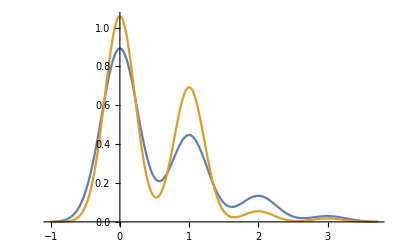

```mathematica
SmoothHistogram[{data, data2}]
```

```mathematica
KolmogorovSmirnovTest[data, data2]
```

0.379575